```mathematica
ClearAll["Global`*"]
```

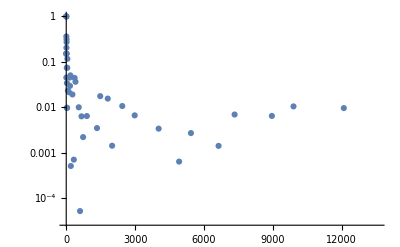

```mathematica
(*Calculo el valor de pi usando el área de un círculo*)
(*Quiero calcular el área A de un círculo de radio 1 centrado en 0inscripto en un cuadrado de lado 1 y área A'*)

ApproximatePi[Nprima_]:=Module[{r,Aprima,N0,x,modulo,A,PiApprox,error},
r = 1;
Aprima = (2 r)^2;
N0 = 0; (*variable N is protected*)
Do[
(*Genero un punto random*)
x=RandomReal[{-1,1},2];
(*Si está dentro del círculo, es decir, su módulo es menor a 1, lo acepto en N*)
modulo = (x[[1]]^2 + x[[2]]^2)^0.5;
If[modulo<1,N0++]
,{j,1,Nprima}];
A = N[ N0 *Aprima /Nprima];
PiApprox = A/r^2;
error = (Pi - PiApprox)/Pi;(*discrepancia*)
error
]
(*Creamos una lista de elementos*)
bin = 0.1;
xmax = 10;
x = Range[0,xmax,bin];
xexp = E^x;
ApproxPiList = ConstantArray[0,Length[x]];
Do[
ApproxPiList[[j]] = ApproximatePi[IntegerPart[xexp[[j]]]]
,{j,1,Length[x]}]
ListLogPlot[Transpose[{xexp,ApproxPiList}]] (*solo el error relativo está en log*)
(*
(1) Con muy pocos puntos el error es cercano a la unidad;
(2) El gráfico cambia cuando vuelvo a ejectura el programa. Esto se debe a que en cada ejecución los números random que aparecen son distintos;
(3)X No hay una relación perfecta entre error y Nprima, es más bien una tendencia;
(4)X A medida que aumenta la cantidad de puntos el error disminuye pero se plancha en 10^-5;

(3) Sí hay una relación entre error y Nprima. Si grafico log log se ve que es una potencia;
(4) No se plancha el error, sino que decae muy lentamente;
(5) Para tener un error relativo de 0.001 no hace falta hacer el cálculo para muchos puntos, con 100.000 alcanza y sobre. Con 1.000.000 obtengo casi el mismo error;
(6) Los griegos estimaron el Pi como 22/7, tiene un error relativo de 0.0004
*)
(N[22/7 ] - Pi )/Pi
```

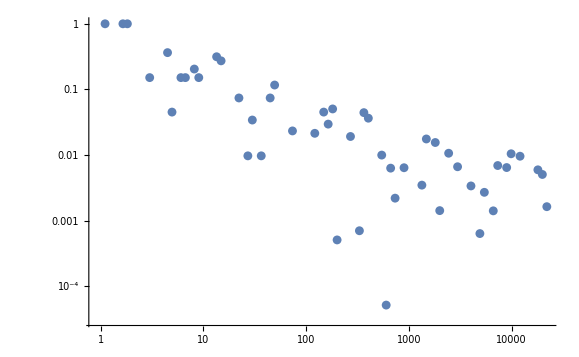

```mathematica
ListLogLogPlot[Transpose[{xexp,ApproxPiList}]] (*gráfica log log*)
```

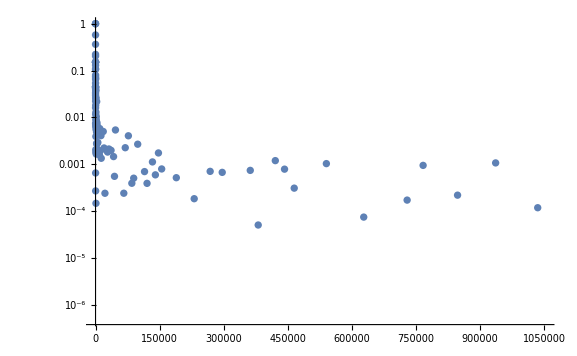

0.000402499